## 0. Wolfram language basics

## Hello

Hello, there! Do you know that person?
                      
Probably, not. However,   does. You can ask her using  function.

```mathematica
Classify["NotablePerson",-Graphics-,"TopProbabilities"]
```

{Stephen Wolfram→0.999898}

Mathematica is famous for its large database and ability to cope with huge amount of problems. For example, she can read a Wikipedia page about herself and, say, count all the letters in the article. Strangely, it contains more “a” then “e”.

```mathematica
LetterCounts[WikipediaData["Wolfram_Mathematica"],IgnoreCase->True][[;;10]]
```

<|a→949,e→925,t→788,i→759,n→701,o→676,r→582,s→552,c→466,l→450|>

However, in our course we will concentrate only on the functionality of  that is related to scientific problems, such as computation of integrals, solving differential equation, working with matrices etc.

## Expressions & Functions

### Expression form

For   . At the beginning it is useful to apply  to new lines of code you see to understand how  looks at the code.

```mathematica
FullForm[x+y z]
```

Plus[x,Times[y,z]]

Another way to represent the expression is via  function.

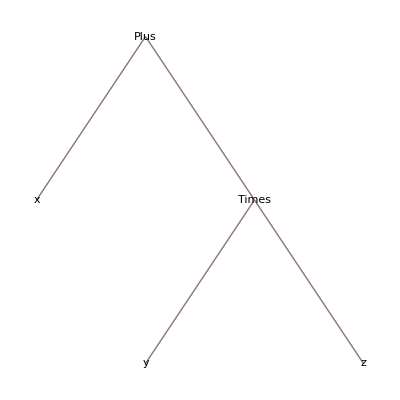

```mathematica
TreeForm[x+y z]
```

You can see that  implicitly each symbolic expression is treated as some function. The most  upper function is called the . Compile the following lines to see what what are the heads of various expressions you can encounter.

```mathematica
Head[x+y z]
```

```mathematica
Head[x]
```

```mathematica
Head[1]
```

```mathematica
Head["Hello"]
```

```mathematica
Head[Series[Sin[x],{x,0,2}]]
```

### Definitions

As customary symbolic expressions may be assigned a value, or generally, any expression.

```mathematica
a=3;
a+2
```

Note that variables with assigned values change their color from blue to black. You can always ask what is the  of the symbol using question mark.

```mathematica
?a
```

```mathematica
f=Sin[x]^2
```

If you like   to forget definition use  function.

```mathematica
ClearAll[a,f]
```

#### Immediate and Delayed Definitions

When you type an expression, by default,  tries to . However, in some cases, you want an expression to be at , and  it to  only when you call. Feel the difference between  and  on the following example.

```mathematica
r=RandomReal[];
r-r
```

```mathematica
r:=RandomReal[];
r-r
```

### Applying functions

As you might have notice  has a lot of syntax sugar -- many ways to call the same command. Here are several ways to apply a function, which are equivalent. This may feel unnecessary, though comes out to be really handy sometimes.

```mathematica
Sin[x]
```

```mathematica
Sin@x
```

```mathematica
x//Sin
```

```mathematica
Sin/@{x}
```

```mathematica
Apply[Sin,{x}]
```

To apply function to the list use . It can be done via many ways as well.

```mathematica
l={1,2,3,4,5};
```

```mathematica
Map[Sin,l]
```

```mathematica
Sin/@l
```

```mathematica
Sin[l]
```

### Function definition

To define a function (in the sense, that you want to plug some expression into another) you use , which looks as follows.

```mathematica
f[x_]=Sin[x]^2;
f[y]
```

```mathematica
F=Sin[x]^2;
F/.{x->y}
```

#### Pure functions

Here is another very useful way to define a function. Examine the syntax of the following expressions.

```mathematica
g=Sin[#]&;
g@(π/7)
```

```mathematica
plus=+##&;
plus[x,y,z]
```

#### Simplify

One more function you’ll find handy working with expressions is . Basically, applies to expression all knowns transformations attempting to minimize some . By default, it is simply a . Here is some expression.

```mathematica
expr=1-Cos[x]^2 Sin[x]^2
```

1-Cos[x]^2 Sin[x]^2

```mathematica
Simplify[expr]
```

1/8 (7+Cos[4 x])

Function  is different from  in the manner that it also knows special function identities.

```mathematica
x Gamma[x]//FullSimplify
```

## Lists and Matrices

```mathematica
ClearAll["`*"]
```

Here several basic operations with arrays, that will come useful.

### Lists

Here are two equivalent definitions.

```mathematica
l={1,2,3,4,5}
```

```mathematica
l=Range[5]
```

To take some element from list use  function or corresponding shortcut.

```mathematica
Part[l,2]
```

```mathematica
l[[2;;4]]
```

```mathematica
l[[-2]]
```

You can find more about operations with lists in the .

#### Associations

```mathematica
a=<|a->1,b->2,c->3,d->4|>
```

<|a→1,b→2,c→3,d→4|>

I named the list and its key the same. Will it lead to an error?

```mathematica
a[[Key[b]]]
```

```mathematica
a[[Key[a]]]
```

### Matrices

Matrix is simply an array of arrays. To show it in customary form use .

```mathematica
m={{Cos[x],Sin[x]},{Sin[x],-Cos[x]}}
```

```mathematica
m//MatrixForm
```

```mathematica
m.m
```

```mathematica
Simplify[%]//MatrixForm
```

For example, you can  vectors and matrices. If you wish you final tensor to have the form of the matrix use .

```mathematica
av=Array[Subscript[a, #]&,{3}];
bv=Array[Subscript[b, #]&,{3}];
cv=Array[Subscript[c, ##]&,{3,3}];
{av//Column,
bv//Column,
cv//Column,
cv//MatrixForm}
```

```mathematica
MatrixForm/@{av⊗bv,Array[Subscript[a, #1] Subscript[b, #2]&,{3,3}]}
```

#### Exercise 0.1

Evaluate matrix exponent ⅇ^(ⅈ(π/2)σ_y), where σ_y is Pauli matrix.

#### Ex. 0.2

Create a function that returns 2n by 2n matrix of the form
(a | a
b | b) (n=1) 	(a | a | a | a
b | b | b | b
a | a | a | a
b | b | b | b) (n=2)
with a, b and size n being arbitrary.

#### Problem 1.1

Construct a  that prefers Sin[x]^n and Cos[x]^n instead of Sin[nx] and Cos[nx].
 Cos[4x] using it.